# K-LC functions

```mathematica
ayMax = 8;
jyMax =50;
```

## Functions

```mathematica
laneChangeMnvAcc=Piecewise[{
{jMax*t,0<=t&& t<=aMax/jMax},
{aMax,aMax/jMax<t&&t<=aMax/jMax+tY},{aMax-jMax*(t-aMax/jMax-tY),aMax/jMax+tY<t&&t<=3aMax/jMax+tY},{-aMax,3aMax/jMax+tY<t&&t<=3aMax/jMax+2tY},{-aMax+jMax*(t-3aMax/jMax-2tY),3aMax/jMax+2tY<t&&t<=4aMax/jMax+2tY},
{0,4aMax/jMax+2tY<t&&t<=5(4aMax/jMax+2tY)}},0];
```

```mathematica
laneChangeMnvDsp=Piecewise[{{(jMax t^3)/6, t≥0&&aMax/jMax≥t}, {(aMax (aMax^2-3 aMax jMax t+3 jMax^2 t^2))/(6 jMax^2), aMax/jMax<t&&aMax/jMax+tY≥t}, {(2 aMax^3-jMax^3 (t-tY)^3+3 aMax^2 jMax (-2 t+tY)+3 aMax jMax^2 (2 t^2-2 t tY+tY^2))/(6 jMax^2), aMax/jMax+tY<t&&(3 aMax)/jMax+tY≥t}, {-(aMax (25 aMax^2+3 aMax jMax (-7 t+8 tY)+3 jMax^2 (t^2-4 t tY+2 tY^2)))/(6 jMax^2), (3 aMax)/jMax+tY<t&&(3 aMax)/jMax+2 tY≥t}, {-(26 aMax^3)/(3 jMax^2)+(aMax^2 (8 t-13 tY))/jMax+1/6 jMax (t-2 tY)^3+aMax (-2 t^2+8 t tY-7 tY^2), (3 aMax)/jMax+2 tY<t&&(4 aMax)/jMax+2 tY≥t}, {(aMax (aMax+jMax tY) (2 aMax+jMax tY))/jMax^2, t>(4 aMax)/jMax+2 tY}, {0, True}}];
```

```mathematica
calcKLC[aLC_,jLC_]:=Module[{nPoints = 100, tYY, nKLC, ayKLC,tFKLC,nF=2.5},

tYY=Solve[(laneChangeMnvDsp[[1,-1,1]]/.{t->(4 aMax)/jMax+2 tY}/.{jMax->jLC,aMax->aLC})==nF,tY,Assumptions->tY>0][[1,1,2]];

tFKLC=(4 aLC)/jLC+2 tYY;

ayKLC=Table[laneChangeMnvAcc/.{jMax->jLC,aMax->aLC,tY->tYY}/.t->tt,{tt,0,tFKLC,tFKLC/(nPoints -1)}];

nKLC=Table[laneChangeMnvDsp/.{jMax->jLC,aMax->aLC,tY->tYY}/.t->tt,{tt,0,tFKLC,tFKLC/(nPoints -1)}];

{tFKLC, nKLC, ayKLC}
]
```

```mathematica
calcKLCTD[tFD_,jLC_]:=Module[{nPoints =100,ttt,aLC, nF=2.5,tmp},

ttt=Quiet@Solve[(laneChangeMnvDsp[[1,-1,1]]/.{aMax->aLC,jMax->jLC}/.{t->(4 aLC)/jLC+2 tY})==nF,tY][[2,1,2]];

aLC=NSolve[(4 aLC)/jLC+2ttt==tFD,aLC,Reals][[1,1,2]];
aLC

(*tmp=calcKLC[aLC,jLC]*)

]
```

```mathematica
tmp=calcKLC[ayMax,jyMax];
tFKLC=tmp[[1]];nKLC=tmp[[2]];ayKLC=tmp[[3]];
```

```mathematica
tFKLC
```

1.28942

```mathematica
calcKLCTD[tFKLC,50]
```

8.

```mathematica
tInfJerkKLC=2Last@Last@Last@Solve[0.5 ay t^2 ==2.5/2,t]/.ay->8
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

1.11803

### plots K-LC

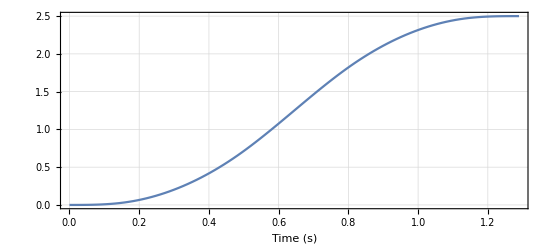

```mathematica
pnLatKLC=ListLinePlot[{
Transpose@{Table[tt,{tt,0,tFKLC,tFKLC/(Length@nKLC-1)}], nKLC}
},
ImageSize->550,AspectRatio->0.45,
FrameLabel->{{None,None}, {Text[Style["Time (s)",15,FontFamily->"Palatino",Black]],Text[Style["Lateral displacement (m)",15,FontFamily->"Palatino",Black]]}},ImageSize->Large,Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
(*FrameTicks->{{{0,1.,2,2.5},None},{{0.5,1,1.5},None}},*)
ImagePadding->{{40,40},{50,30}},
FrameTicksStyle->{{14,Black},14}]
```

```mathematica
(*Export["/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/pnLatKLC.png", Rasterize[pnLatKLC,"Image",RasterSize->3000]]*)
```

```mathematica
laneChangeMnvAcc/.t->1
```

Piecewise[{{jMax, 1≤aMax/jMax}, {aMax, aMax/jMax<1&&1≤aMax/jMax+tY}, {aMax-jMax (1-aMax/jMax-tY), aMax/jMax+tY<1&&1≤(3 aMax)/jMax+tY}, {-aMax, (3 aMax)/jMax+tY<1&&1≤(3 aMax)/jMax+2 tY}, {-aMax+jMax (1-(3 aMax)/jMax-2 tY), (3 aMax)/jMax+2 tY<1&&1≤(4 aMax)/jMax+2 tY}, {0, True}}]

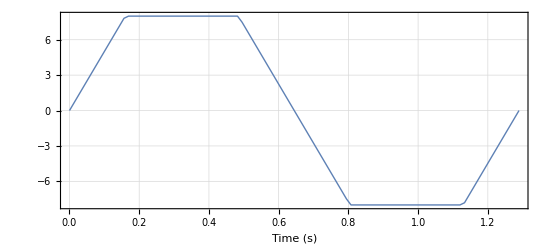

```mathematica
paLatKLC=ListLinePlot[Transpose@{Table[tt,{tt,0,tFKLC,tFKLC/(Length@nKLC-1)}], ayKLC},
ImageSize->550,AspectRatio->0.45,
FrameLabel->{{None,None}, {Text[Style["Time (s)",15,FontFamily->"Palatino",Black]],Text[Style["Lateral acceleration (m/s^2)",15,FontFamily->"Palatino",Black]]}},PlotStyle->Thick,Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
(*FrameTicks->{{{-5,-2.5,0,2.5,5},None},{{0.5,1,1.5},None}},*)
ImagePadding->{{40,40},{50,30}},
FrameTicksStyle->{{14,Black},14}]
```

```mathematica
(*Export["/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/paLatKLC.png", Rasterize[paLatKLC,"Image",RasterSize->3000]]*)
```

```mathematica
calcKLC[8.,10^10][[1]]
```

1.11803

```mathematica
(tFKLC-calcKLC[8.,10^10][[1]])/tFKLC
```

0.13292

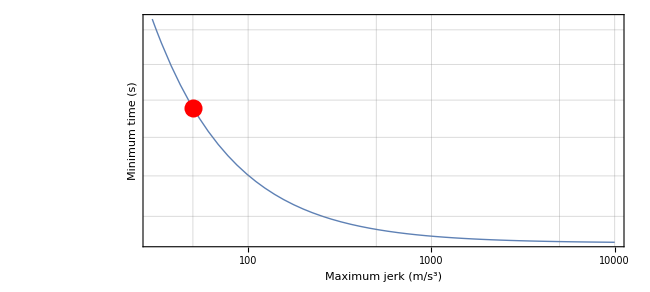

```mathematica
LogLogPlot[calcKLC[8.,jj][[1]],{jj,30,10000},PlotRange->All,
Epilog->{PointSize[0.02],Red,Point[{Log@jyMax,Log@tFKLC}]}
,ImageSize->650,AspectRatio->0.45,
FrameLabel->{{Text[Style["Minimum time (s)",15,FontFamily->"Palatino",Black]],None}, {Text[Style["Maximum jerk (m/s^3)",15,FontFamily->"Palatino",Black]],None}},PlotStyle->Thick,Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
(*FrameTicks->{{{-5,-2.5,0,2.5,5},None},{{0.5,1,1.5},None}},*)
ImagePadding->{{60,60},{50,30}},
FrameTicksStyle->{{14,Black},14}]
```

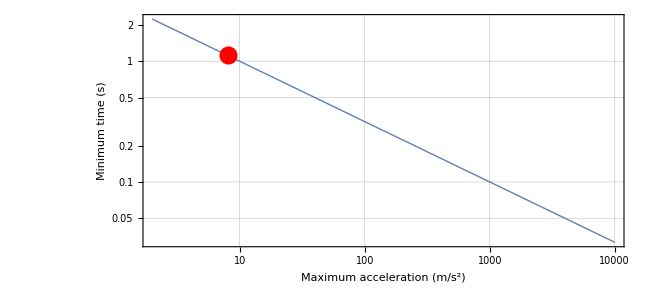

```mathematica
LogLogPlot[calcKLC[ay,10^10][[1]],{ay,2,10000},PlotRange->All,
Epilog->{PointSize[0.02],Red,Point[{Log@ayMax,Log@tInfJerkKLC}]}
,ImageSize->650,AspectRatio->0.45,
FrameLabel->{{Text[Style["Minimum time (s)",15,FontFamily->"Palatino",Black]],None}, {Text[Style["Maximum acceleration (m/s^2)",15,FontFamily->"Palatino",Black]],None}},PlotStyle->Thick,Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
(*FrameTicks->{{{-5,-2.5,0,2.5,5},None},{{0.5,1,1.5},None}},*)
ImagePadding->{{60,60},{50,30}},
FrameTicksStyle->{{14,Black},14}]
```

```mathematica
pKLCajy=ContourPlot[calcKLC[ay,jy][[1]],{ay,2,20},{jy,10,200},PlotRange->Automatic,
Epilog->{PointSize[0.02],Red,Point[{ayMax,jyMax}]},
MaxRecursion->2,Contours->15,PlotLegends->Automatic,
ContourLabels->Function[{x,y,z},Text[Framed[z,Background->White],{x,y}]],
ImageSize->650,AspectRatio->0.45,
FrameLabel->{{Text[Style["Maximum jerk (s)",15,FontFamily->"Palatino",Black]],None}, {Text[Style["Maximum acceleration (m/s^2)",15,FontFamily->"Palatino",Black]],None}},Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
(*FrameTicks->{{{-5,-2.5,0,2.5,5},None},{{0.5,1,1.5},None}},*)
ImagePadding->{{60,60},{50,30}},
FrameTicksStyle->{{14,Black},14}]
```

$Aborted

# Multiple analysis

## Load data

```mathematica
ocpC = Import[NotebookDirectory[]<>"results_lane_change_T_vehs.csv"]; ocpC//TableForm
```

vel | Abe | Lee | Reina | Lundahl | Soudbakksh | K-LC | Braking
5 | 2.65742 | 2.50018 | 2.10268 | 2.52456 | 2.87674 | 1.28942 | 0.525
7.5 | 1.74481 | 1.58977 | 1.37513 | 1.60883 | 1.7468 | 1.28942 | 0.8375
10 | 1.3488 | 1.48326 | 1.29755 | 1.41198 | 1.41087 | 1.28942 | 1.15
12.5 | 1.30785 | 1.4834 | 1.28049 | 1.41032 | 1.39014 | 1.28942 | 1.4625
15 | 1.27925 | 1.49434 | 1.26725 | 1.40939 | 1.38139 | 1.28942 | 1.775
17.5 | 1.27292 | 1.50713 | 1.25864 | 1.41612 | 1.38413 | 1.28942 | 2.0875
20 | 1.26879 | 1.51865 | 1.25922 | 1.42273 | 1.38626 | 1.28942 | 2.4
22.5 | 1.26489 | 1.52663 | 1.26215 | 1.42866 | 1.39071 | 1.28942 | 2.7125
25 | 1.26104 | 1.53296 | 1.26617 | 1.43811 | 1.39127 | 1.28942 | 3.025
27.5 | 1.26505 | 1.54731 | 1.27011 | 1.44889 | 1.39567 | 1.28942 | 3.3375
30 | 1.26955 | 1.55926 | 1.27405 | 1.4579 | 1.40328 | 1.28942 | 3.65
32.5 | 1.2743 | 1.56879 | 1.27752 | 1.46585 | 1.40945 | 1.28942 | 3.9625
35 | 1.27811 | 1.57612 | 1.28046 | 1.47207 | 1.41428 | 1.28942 | 4.275
37.5 | 1.28104 | 1.58146 | 1.28278 | 1.47671 | 1.41818 | 1.28942 | 4.5875
40 | 1.28313 | 1.58498 | 1.28439 | 1.47989 | 1.42127 | 1.28942 | 4.9

```mathematica
header=ocpC[[1]];
label=header[[2;;-1]];
vel=ocpC[[2;;-1,1]];
tVel =ocpC[[2;;-1,2;;-2]];
tBrk = ocpC[[2;;-1,-1]];
sVel =tVel vel;
```

```mathematica
tVel//TableForm
```

2.65742 | 2.50018 | 2.10268 | 2.52456 | 2.87674 | 1.28942
1.74481 | 1.58977 | 1.37513 | 1.60883 | 1.7468 | 1.28942
1.3488 | 1.48326 | 1.29755 | 1.41198 | 1.41087 | 1.28942
1.30785 | 1.4834 | 1.28049 | 1.41032 | 1.39014 | 1.28942
1.27925 | 1.49434 | 1.26725 | 1.40939 | 1.38139 | 1.28942
1.27292 | 1.50713 | 1.25864 | 1.41612 | 1.38413 | 1.28942
1.26879 | 1.51865 | 1.25922 | 1.42273 | 1.38626 | 1.28942
1.26489 | 1.52663 | 1.26215 | 1.42866 | 1.39071 | 1.28942
1.26104 | 1.53296 | 1.26617 | 1.43811 | 1.39127 | 1.28942
1.26505 | 1.54731 | 1.27011 | 1.44889 | 1.39567 | 1.28942
1.26955 | 1.55926 | 1.27405 | 1.4579 | 1.40328 | 1.28942
1.2743 | 1.56879 | 1.27752 | 1.46585 | 1.40945 | 1.28942
1.27811 | 1.57612 | 1.28046 | 1.47207 | 1.41428 | 1.28942
1.28104 | 1.58146 | 1.28278 | 1.47671 | 1.41818 | 1.28942
1.28313 | 1.58498 | 1.28439 | 1.47989 | 1.42127 | 1.28942

```mathematica
s2brake[v_]:=Module[{a=8,j=40,tamax, vamax,samax,stmp},
	tamax=a/j;
	vamax = v-a tamax - 0.5 j tamax^2;
	stmp=v tamax -0.5 a tamax^2 - 0.5 1/3 j tamax^3;
	If[vamax <0,
		samax=N@(v t -0.5 a t^2 - 0.5 1/3 j t^3)/.t->(-1. a+Sqrt[a^2+2. j v])/j,
		samax=stmp+( vamax t - 0.5a t^2)/.t->vamax/a
	];
	samax
]
```

## Plot data

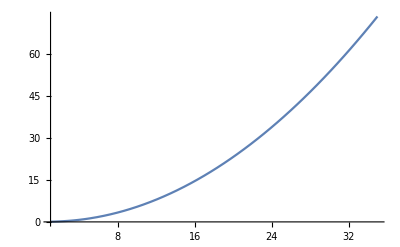

```mathematica
Plot[s2brake[v],{v,1,35}]
```

```mathematica
velF=Table[vv,{vv,vel[[1]],vel[[-1]],2}];
sBrkF=Table[s2brake[velF[[i]]],{i,1,Length@velF}];
```

```mathematica
sBrk=Table[s2brake[vel[[i]]],{i,1,Length@vel}];
```

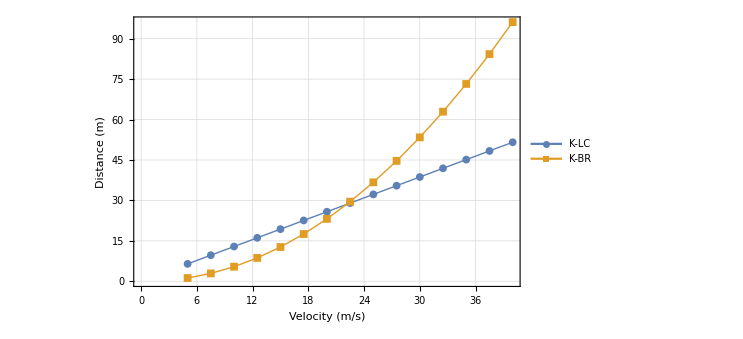

```mathematica
ListLinePlot[{
Transpose@{vel,tFKLC  vel},
   Transpose@{vel,sBrk}},
PlotLegends->Placed[LineLegend[{"K-LC","K-BR"},LegendMarkerSize->10,LegendFunction->Frame,Background->White],{0.14,0.7}],ImageSize->550,PlotMarkers->{Automatic,8},PlotStyle->Thick,
FrameLabel->{Text[Style["Velocity (m/s)",15,FontFamily->"Palatino",Black]],Text[Style["Distance (m)",15,FontFamily->"Palatino",Black]]},Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
(*FrameTicks->{{{-5,-2.5,0,2.5,5},None},{{0.5,1,1.5},None}},*)
ImagePadding->{{50,50},{50,10}},
FrameTicksStyle->{{14,Black},14}]
```

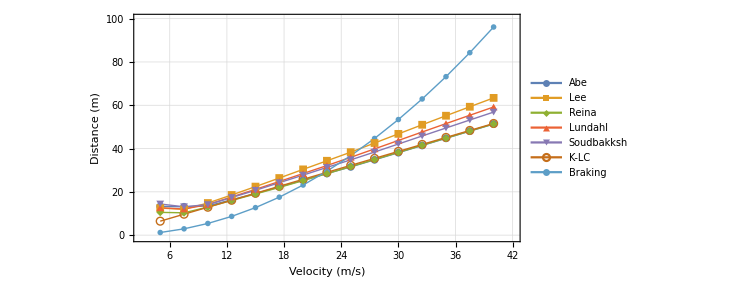

```mathematica
pS=ListLinePlot[{
Transpose@{vel,sVel[[All,1]]},
Transpose@{vel,sVel[[All,2]] },
Transpose@{vel,sVel[[All,3]] },
Transpose@{vel,sVel[[All,4]] },
Transpose@{vel,sVel[[All,5]] },
Transpose@{vel,sVel[[All,6]] },
Transpose@{vel,sBrk}},
PlotRange->{{3,42},{-1,100}},
PlotLegends->Placed[LineLegend[label,LegendMarkerSize->10,LegendLayout->"Row",LegendFunction->Frame,Background->White],{0.28,0.82}],ImageSize->550,PlotMarkers->{Automatic,8},PlotStyle->Thick,AspectRatio->0.52,
FrameLabel->{Text[Style["Velocity (m/s)",15,FontFamily->"Palatino",Black]],Text[Style["Distance (m)",15,FontFamily->"Palatino",Black]]},Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
(*FrameTicks->{{{-5,-2.5,0,2.5,5},None},{{0.5,1,1.5},None}},*)
ImagePadding->{{50,50},{50,10}},
FrameTicksStyle->{{14,Black},14}]
```

```mathematica
(*Export["/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/pS.png", Rasterize[pS,"Image",RasterSize->3000]]*)
```

/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/pS.png

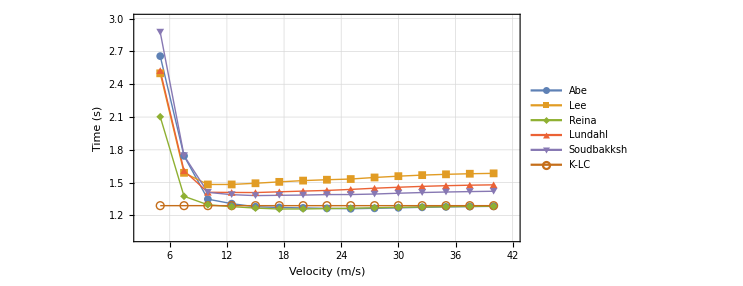

```mathematica
pT=ListLinePlot[{
Transpose@{vel,tVel[[All,1]] },
Transpose@{vel,tVel[[All,2]] },
Transpose@{vel,tVel[[All,3]] },
Transpose@{vel,tVel[[All,4]] },
Transpose@{vel,tVel[[All,5]] },
Transpose@{vel,tVel[[All,6]] }(*,
Transpose@{vel,tBrk}*)
},PlotRange->{{3,42},{1,3}},PlotLegends->
Placed[LineLegend[label,LegendLayout->{"Row",1},LegendMarkerSize->10,LegendFunction->Frame,Background->White],{0.55,0.9}],
ImageSize->550,PlotMarkers->{Automatic,8},PlotStyle->Thick,AspectRatio->0.52,
FrameLabel->{Text[Style["Velocity (m/s)",15,FontFamily->"Palatino",Black]],Text[Style["Time (s)",15,FontFamily->"Palatino",Black]]},Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
(*FrameTicks->{{{-5,-2.5,0,2.5,5},None},{{0.5,1,1.5},None}},*)
ImagePadding->{{50,50},{50,10}},
FrameTicksStyle->{{14,Black},14}]
```

```mathematica
(*Export["/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/pT.png", Rasterize[pT,"Image",RasterSize->3000]]*)
```

/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/pT.png

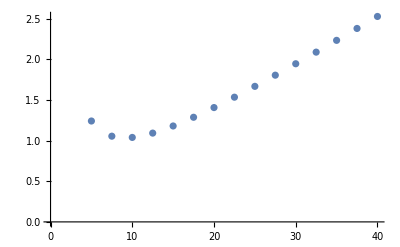

```mathematica
ListPlot[Transpose@{vel,(sBrk+5)/vel}]
```

```mathematica
lV = 5;
```

```mathematica
label
```

{Abe,Lee,Reina,Lundahl,Soudbakksh,K-LC,Braking}

```mathematica
sVel[[All,6]]
```

{6.4471,9.67065,12.8942,16.1178,19.3413,22.5649,25.7884,29.012,32.2355,35.4591,38.6826,41.9062,45.1297,48.3533,51.5768}

```mathematica
sVelKLC=Append[tVel[[All,6]],tVel[[All,6]][[1]]]Append[vel,70];
```

```mathematica
pTTCReina =ListLinePlot[{
Transpose@{vel,(sVel[[All,6]]+lV)/vel},Transpose@{velF,(sBrkF+lV)/velF},
Transpose@{vel,(sVel[[All,3]]+lV)/vel}},

Filling->{1->{Top,Opacity[0.1]},2->Top,3->Top,
1->{{2},{{HatchFilling[-Pi/4,5,15],Opacity[0.2,Blue]},{HatchFilling[0,5,15],Opacity[0.4,Black]}}},
1->{{3},{{HatchFilling[Pi/2,5,15],Opacity[0.2,Red]},{HatchFilling[0,5,10],Opacity[0.3,Red]}}}
},

PlotStyle->{{ColorData[97][1],Thick},{ColorData[97][2],Thick},{ColorData[97][3],Thick},Transparent},

PlotRange->{{10,38},{1,2.5}},
ImageSize->550,PlotMarkers->{Automatic,8},PlotStyle->{Thickness[0.006]},
FrameLabel->{Text[Style["Velocity (m/s)",15,FontFamily->"Palatino",Black]],Text[Style["TTC (s)",15,FontFamily->"Palatino",Black]]},Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
PlotLegends->
Placed[LineLegend[{"K-LC","Braking","Reina D-LC"},LegendMarkerSize->10,LegendFunction->Frame, Background->White],{0.12,0.85}],ImageSize->550,PlotMarkers->{Automatic,8},
ImagePadding->{{50,50},{50,10}},
FrameTicksStyle->{{14,Black},14}

]
```

-Graphics-

```mathematica
(*Export["/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/pTTCReina.png", Rasterize[pTTCReina,"Image",RasterSize->3000]]*)
```

```mathematica
pSAVEReina=ListLinePlot[{
Transpose@{Append[sVel[[All,6]]+.5lV,120],Append[vel,50]},
Transpose@{sBrkF+lV,velF},
Transpose@{Append[sVel[[All,3]]+.5lV,120],Append[vel,50]}
},

Filling->{1->{Bottom,Opacity[0.1]},2->Bottom,3->Bottom,
1->{{2},{{HatchFilling[15,5,15],Opacity[0.2,Blue]},{HatchFilling[Pi/2,5,15],Opacity[0.4,Black]}}},
1->{{3},{{HatchFilling[15,5,20],Opacity[0.2,Red]},{HatchFilling[0,5,10],Opacity[0.3,Red]}}}
},
PlotStyle->{{ColorData[97][1],Thick},{ColorData[97][2],Thick},{ColorData[97][3],Thick},Transparent},

PlotRange->{{10,85},{0.5,40}},
ImageSize->550,PlotMarkers->{Automatic,8},PlotStyle->{Thickness[0.006]},
FrameLabel->{Text[Style["Clearance to obstacle (m)",15,FontFamily->"Palatino",Black]],Text[Style["Velocity (m/s)",15,FontFamily->"Palatino",Black]]},Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
PlotLegends->
Placed[LineLegend[{"K-LC","Braking","Reina D-LC"},LegendMarkerSize->10,LegendFunction->Frame, Background->White],{0.12,0.85}],ImageSize->550,PlotMarkers->{Automatic,8},
ImagePadding->{{50,50},{50,10}},
FrameTicksStyle->{{14,Black},14}]
```

-Graphics-

```mathematica
(*Export["/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/pSAVEReina.png", Rasterize[pSAVEReina,"Image",RasterSize->3000]]*)
```

```mathematica
pTTCLee =ListLinePlot[{
Transpose@{vel,(sVel[[All,6]]+lV)/vel},Transpose@{velF,(sBrkF+lV)/velF},
Transpose@{vel,(sVel[[All,2]]+lV)/vel}},

Filling->{1->{Top,Opacity[0.1]},2->Top,3->Top,
1->{{2},{{HatchFilling[-Pi/4,5,15],Opacity[0.2,Blue]},{HatchFilling[0,5,15],Opacity[0.4,Black]}}},
1->{{3},{{HatchFilling[Pi/2,5,15],Opacity[0.2,Red]},{HatchFilling[0,5,10],Opacity[0.3,Red]}}}
},

PlotStyle->{{ColorData[97][1],Thick},{ColorData[97][2],Thick},{ColorData[97][3],Thick},Transparent},

PlotRange->{{10,38},{1,2.5}},
ImageSize->550,PlotMarkers->{Automatic,8},PlotStyle->{Thickness[0.006]},
FrameLabel->{Text[Style["Velocity (m/s)",15,FontFamily->"Palatino",Black]],Text[Style["TTC (s)",15,FontFamily->"Palatino",Black]]},Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
PlotLegends->
Placed[LineLegend[{"K-LC","Braking","Lee D-LC"},LegendMarkerSize->10,LegendFunction->Frame, Background->White],{0.11,0.85}],ImageSize->550,PlotMarkers->{Automatic,8},
ImagePadding->{{50,50},{50,10}},
FrameTicksStyle->{{14,Black},14}

]
```

-Graphics-

```mathematica
(*Export["/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/pTTCLee.png", Rasterize[pTTCLee,"Image",RasterSize->3000]]*)
```

```mathematica
pSAVELee=ListLinePlot[{
Transpose@{Append[sVel[[All,6]],120]+0.5lV,Append[vel,50]},
Transpose@{sBrkF+lV,velF},
Transpose@{Append[sVel[[All,2]],120]+0.5lV,Append[vel,50]}
},

Filling->{1->{Bottom,Opacity[0.1]},2->Bottom,3->Bottom,
1->{{2},{{HatchFilling[15,5,15],Opacity[0.2,Blue]},{HatchFilling[Pi/2,5,15],Opacity[0.4,Black]}}},
1->{{3},{{HatchFilling[15,5,20],Opacity[0.2,Red]},{HatchFilling[0,5,10],Opacity[0.3,Red]}}}
},
PlotStyle->{{ColorData[97][1],Thick},{ColorData[97][2],Thick},{ColorData[97][3],Thick},Transparent},

PlotRange->{{10,85},{0.5,40}},
ImageSize->550,PlotMarkers->{Automatic,8},PlotStyle->{Thickness[0.006]},
FrameLabel->{Text[Style["Clearance to obstacle (m)",15,FontFamily->"Palatino",Black]],Text[Style["Velocity (m/s)",15,FontFamily->"Palatino",Black]]},Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
PlotLegends->
Placed[LineLegend[{"K-LC","Braking","Lee D-LC"},LegendMarkerSize->10,LegendFunction->Frame, Background->White],{0.11,0.85}],ImageSize->550,PlotMarkers->{Automatic,8},
ImagePadding->{{50,50},{50,10}},
FrameTicksStyle->{{14,Black},14}]
```

-Graphics-

```mathematica
(*Export["/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/pSAVELee.png", Rasterize[pSAVELee,"Image",RasterSize->3000]]*)
```

## Equivalent K-LC acceleration

```mathematica
tEq=Transpose@Join[Transpose@tVel[[3;;-1,1;;-1]],{tBrk[[3;;-1]]}];tEq//TableForm
```

1.3488 | 1.48326 | 1.29755 | 1.41198 | 1.41087 | 1.28942 | 1.15
1.30785 | 1.4834 | 1.28049 | 1.41032 | 1.39014 | 1.28942 | 1.4625
1.27925 | 1.49434 | 1.26725 | 1.40939 | 1.38139 | 1.28942 | 1.775
1.27292 | 1.50713 | 1.25864 | 1.41612 | 1.38413 | 1.28942 | 2.0875
1.26879 | 1.51865 | 1.25922 | 1.42273 | 1.38626 | 1.28942 | 2.4
1.26489 | 1.52663 | 1.26215 | 1.42866 | 1.39071 | 1.28942 | 2.7125
1.26104 | 1.53296 | 1.26617 | 1.43811 | 1.39127 | 1.28942 | 3.025
1.26505 | 1.54731 | 1.27011 | 1.44889 | 1.39567 | 1.28942 | 3.3375
1.26955 | 1.55926 | 1.27405 | 1.4579 | 1.40328 | 1.28942 | 3.65
1.2743 | 1.56879 | 1.27752 | 1.46585 | 1.40945 | 1.28942 | 3.9625
1.27811 | 1.57612 | 1.28046 | 1.47207 | 1.41428 | 1.28942 | 4.275
1.28104 | 1.58146 | 1.28278 | 1.47671 | 1.41818 | 1.28942 | 4.5875
1.28313 | 1.58498 | 1.28439 | 1.47989 | 1.42127 | 1.28942 | 4.9

```mathematica
percRedK=tEq;
```

```mathematica
Table[percRedK[[i,j]]=8(8-calcKLCTD[tEq[[i,j]],50]),{i,1,Length@tEq},{j,1Length@tEq[[1]]}]//TableForm
```

Part::partw: Part 1 of {} does not exist.

8.68267 | 21.5681 | 1.36749 | 15.5666 | 15.4604 | -0.000799731 | 8 (8-{}⟦1,1,2⟧)
3.00681 | 21.5785 | -1.58837 | 15.4076 | 13.39 | -0.000799731 | 19.9698
-1.81641 | 22.3781 | -4.12926 | 15.3181 | 12.4627 | -0.000799731 | 36.4739
-3.01159 | 23.2788 | -5.92106 | 15.9587 | 12.7567 | -0.000799731 | 44.7543
-3.82106 | 24.0604 | -5.7965 | 16.5723 | 12.9829 | -0.000799731 | 49.6841
-4.60856 | 24.5862 | -5.17603 | 17.11 | 13.4492 | -0.000799731 | 52.8999
-5.40939 | 24.9946 | -4.34753 | 17.9432 | 13.5073 | -0.000799731 | 55.1273
-4.57579 | 25.893 | -3.55968 | 18.8601 | 13.9591 | -0.000799731 | 56.739
-3.67025 | 26.6136 | -2.7943 | 19.6005 | 14.7219 | -0.000799731 | 57.9449
-2.74646 | 27.1713 | -2.13782 | 20.2352 | 15.3239 | -0.000799731 | 58.8717
-2.02777 | 27.5904 | -1.59387 | 20.7201 | 15.7852 | -0.000799731 | 59.5999
-1.48785 | 27.8906 | -1.17226 | 21.0755 | 16.1516 | -0.000799731 | 60.1828
-1.10922 | 28.0861 | -0.883502 | 21.3159 | 16.438 | -0.000799731 | 60.6566

```mathematica
percRedKInf=tEq;
Table[percRedKInf[[i,j]]=8(8-calcKLCTD[tEq[[i,j]],10000]),{i,1,Length@tEq},{j,1Length@tEq[[1]]}]//TableForm
```

19.9902 | 27.615 | 16.4402 | 23.8448 | 23.7815 | 15.8377 | 3.42875
17.1874 | 27.6219 | 15.1627 | 23.7501 | 22.5717 | 15.8377 | 26.5738
15.0678 | 28.1531 | 14.1353 | 23.6969 | 22.0447 | 15.8377 | 38.5991
14.5792 | 28.7595 | 13.4498 | 24.0795 | 22.2108 | 15.8377 | 45.6375
14.2565 | 29.2925 | 13.4964 | 24.45 | 22.3393 | 15.8377 | 50.1091
13.9488 | 29.6547 | 13.7309 | 24.7779 | 22.6057 | 15.8377 | 53.1259
13.6423 | 29.938 | 14.0501 | 25.2922 | 22.6391 | 15.8377 | 55.2568
13.9615 | 30.5674 | 14.36 | 25.8666 | 22.8998 | 15.8377 | 56.8176
14.3161 | 31.0783 | 14.667 | 26.337 | 23.3448 | 15.8377 | 57.9949
14.6864 | 31.4774 | 14.935 | 26.7448 | 23.7004 | 15.8377 | 58.9048
14.9804 | 31.7794 | 15.1604 | 27.0593 | 23.9754 | 15.8377 | 59.6225
15.2047 | 31.9968 | 15.3371 | 27.2913 | 24.1955 | 15.8377 | 60.1986
15.3637 | 32.1389 | 15.4592 | 27.449 | 24.3686 | 15.8377 | 60.668

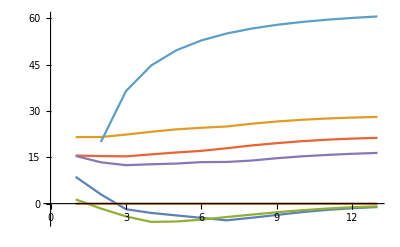

```mathematica
ListLinePlot@Transpose@percRedK
```

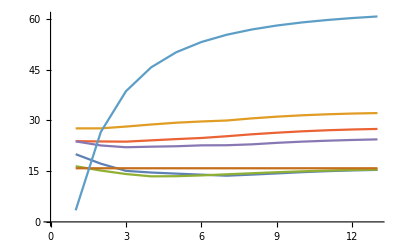

```mathematica
ListLinePlot@Transpose@percRedKInf
```

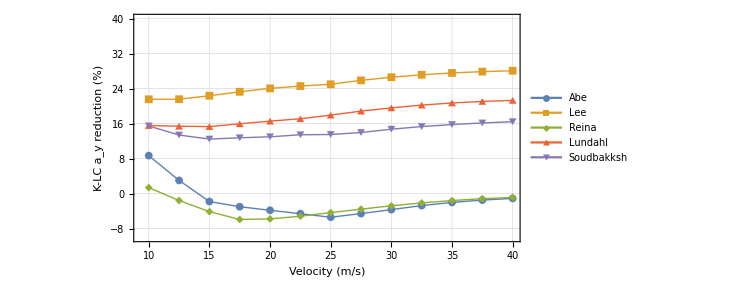

```mathematica
pRED=ListLinePlot[{
Transpose@{vel[[3;;-1]],percRedK[[All,1]]},
Transpose@{vel[[3;;-1]],percRedK[[All,2]] },
Transpose@{vel[[3;;-1]],percRedK[[All,3]] },
Transpose@{vel[[3;;-1]],percRedK[[All,4]] },
Transpose@{vel[[3;;-1]],percRedK[[All,5]] }(*,
Transpose@{vel[[3;;-2]],percRedK[[All,6]] }*)
},
PlotLegends->Placed[LineLegend[{Flatten@{label[[1;;-3]],label[[-1]]}},LegendMarkerSize->8,LegendLayout->"Row",LegendFunction->Frame,Background->White],{0.5,0.9}],ImageSize->550,PlotMarkers->{Automatic,8},PlotStyle->Thick,PlotRange->{-10.,40},AspectRatio->0.52,
FrameLabel->{Text[Style["Velocity (m/s)",15,FontFamily->"Palatino",Black]],Text[Style["K-LC a_y reduction (%)",15,FontFamily->"Palatino",Black]]},Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
(*FrameTicks->{{{-5,-2.5,0,2.5,5},None},{{0.5,1,1.5},None}},*)
ImagePadding->{{55,55},{50,10}},
FrameTicksStyle->{{14,Black},14}]
```

```mathematica
(*Export["/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/pRED.png", Rasterize[pRED,"Image",RasterSize->3000]]*)
```

/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/pRED.png

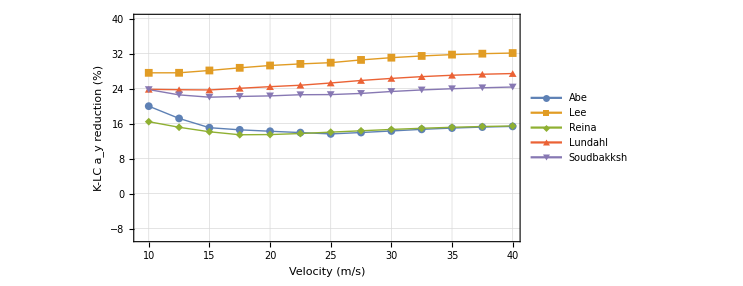

```mathematica
pREDInf=ListLinePlot[{
Transpose@{vel[[3;;-1]],percRedKInf[[All,1]]},
Transpose@{vel[[3;;-1]],percRedKInf[[All,2]] },
Transpose@{vel[[3;;-1]],percRedKInf[[All,3]] },
Transpose@{vel[[3;;-1]],percRedKInf[[All,4]] },
Transpose@{vel[[3;;-1]],percRedKInf[[All,5]] }(*,
Transpose@{vel[[3;;-2]],percRedK[[All,6]] }*)
},
PlotLegends->Placed[LineLegend[{Flatten@{label[[1;;-3]],label[[-1]]}},LegendMarkerSize->8,LegendLayout->"Row",LegendFunction->Frame,Background->White],{0.5,0.1}],ImageSize->550,PlotMarkers->{Automatic,8},PlotStyle->Thick,PlotRange->{-10.,40},AspectRatio->0.52,
FrameLabel->{Text[Style["Velocity (m/s)",15,FontFamily->"Palatino",Black]],Text[Style["K-LC a_y reduction (%)",15,FontFamily->"Palatino",Black]]},Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
(*FrameTicks->{{{-5,-2.5,0,2.5,5},None},{{0.5,1,1.5},None}},*)
ImagePadding->{{55,55},{50,10}},
FrameTicksStyle->{{14,Black},14}]
```

```mathematica
(*Export["/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/pREDInf.png", Rasterize[pREDInf,"Image",RasterSize->3000]]*)
```

/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/pREDInf.png

```mathematica
Table[calcKLCTD[t,60],{t,Min@Flatten@tVel,Max@Flatten@tVel,0.2}]
```

{calcKLCTD[1.25864,60],calcKLCTD[1.45864,60],calcKLCTD[1.65864,60],calcKLCTD[1.85864,60],calcKLCTD[2.05864,60],calcKLCTD[2.25864,60],calcKLCTD[2.45864,60],calcKLCTD[2.65864,60],calcKLCTD[2.85864,60]}

```mathematica
Plot[calcKLCTD[t,60],{t,Min@Flatten@tVel,Max@Flatten@tVel}]
```

-Graphics-

# Single analysis

## Load data

```mathematica
ocpU = Import[NotebookDirectory[]<>"results_control_jerk_relax.txt", "Table"];
ocpS = Import[NotebookDirectory[]<>"results_states_jerk_relax.txt", "Table"];
ocpT = Import[NotebookDirectory[]<>"results_params_jerk_relax.txt", "Table"];
tF=ocpT[[1,3]]
```

1.56054

```mathematica
ocpUReina = Import[NotebookDirectory[]<>"results_control_jerk_relax_reina.txt", "Table"];
ocpSReina = Import[NotebookDirectory[]<>"results_states_jerk_relax_reina.txt", "Table"];
ocpTReina = Import[NotebookDirectory[]<>"results_params_jerk_relax_reina.txt", "Table"];
tFReina=ocpTReina[[1,3]]
```

1.27472

```mathematica
Table[tt,{tt,1,21,0.5}]
```

{1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,20.,20.5,21.}

```mathematica
Append[ocpS[[All,3]],2.5]
```

{0.,0.0276245,0.0792997,0.146088,0.228203,0.332328,0.464671,0.625579,0.802511,0.98442,1.17275,1.36852,1.56394,1.74798,1.91409,2.05425,2.17042,2.27842,2.37835,2.44939,2.5,2.5}

```mathematica
nTMP =Interpolation[Append[ocpS[[All,3]],2.51]][Table[tt,{tt,1,22,0.6}]];
```

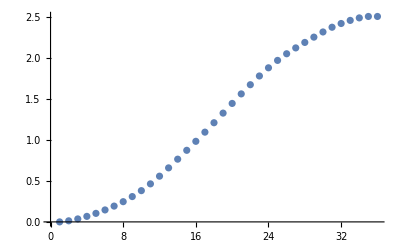

```mathematica
ListPlot@nTMP
```

```mathematica
n=Interpolation[ocpS[[All,3]]][Table[tt,{tt,1,21,0.5}]];
psi = Interpolation[ocpS[[All,4]]][Table[tt,{tt,1,21,0.5}]];
omega=Interpolation[ocpS[[All,5]]][Table[tt,{tt,1,21,0.5}]];
beta=Interpolation[ocpS[[All,6]]][Table[tt,{tt,1,21,0.5}]];
aF = Interpolation[ocpS[[All,7]]][Table[tt,{tt,1,21,0.5}]];
aR = Interpolation[ocpS[[All,8]]][Table[tt,{tt,1,21,0.5}]];
delta =Interpolation[ocpS[[All,9]]][Table[tt,{tt,1,21,0.5}]];
u =Interpolation[ocpU[[All,3]]][Table[tt,{tt,1,21,0.5}]];
```

```mathematica
nReina=Interpolation[ocpSReina[[All,3]]][Table[tt,{tt,1,21,0.5}]];
psiReina = Interpolation[ocpSReina[[All,4]]][Table[tt,{tt,1,21,0.5}]];
omegaReina=Interpolation[ocpSReina[[All,5]]][Table[tt,{tt,1,21,0.5}]];
betaReina=Interpolation[ocpSReina[[All,6]]][Table[tt,{tt,1,21,0.5}]];
aFReina = Interpolation[ocpSReina[[All,7]]][Table[tt,{tt,1,21,0.5}]];
aRReina = Interpolation[ocpSReina[[All,8]]][Table[tt,{tt,1,21,0.5}]];
deltaReina =Interpolation[ocpSReina[[All,9]]][Table[tt,{tt,1,21,0.5}]];
uReina =Interpolation[ocpUReina[[All,3]]][Table[tt,{tt,1,21,0.5}]];
```

```mathematica
ay=(-(1+2*(lf*Kf-lr*Kr)/(m*V*V))*omega-2*(Kf+Kr)/(m*V)*beta+2*Kf/(m*V)*delta+omega*V)/.{m->2200,lf->1.37,lr->1.58,Kr->57930,Kf->42040,V->30};
```

```mathematica
ayReina=(-(1+2*(lf*Kf-lr*Kr)/(m*V*V))*omegaReina-2*(Kf+Kr)/(m*V)*betaReina+2*Kf/(m*V)*deltaReina+omegaReina*V)/.{m->1400,lf->1.22,lr->1.04,Kr->58620,Kf->71360,V->30};
```

```mathematica
s = Accumulate[30 (1-beta psi)][[-1]]/(Length@beta ) tF
```

46.9086

## Plots OCP 30

```mathematica
pAspect = 0.35;
```

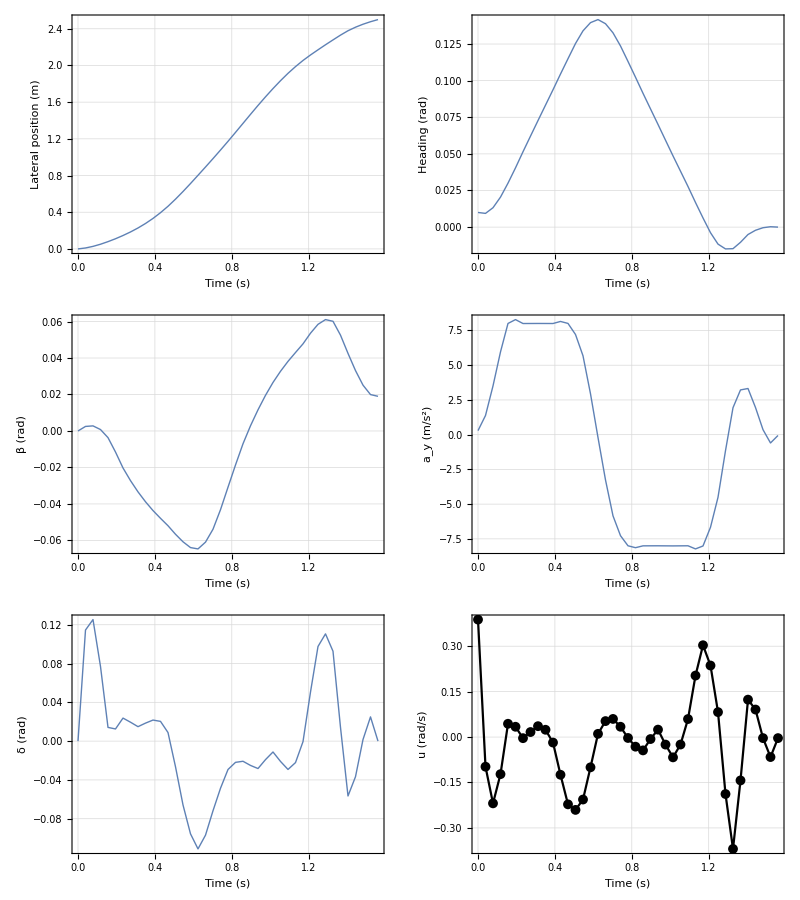

```mathematica
pN=ListLinePlot[Transpose@{Table[tt,{tt,0,tF,tF/(Length@n-1)}], n},
ImageSize->550,AspectRatio->pAspect,
FrameLabel->{{Text[Style["Lateral position (m)",15,FontFamily->"Palatino",Black]],None}, {Text[Style["Time (s)",15,FontFamily->"Palatino",Black]],None}},PlotStyle->Thick,Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
(*FrameTicks->{{{-5,-2.5,0,2.5,5},None},{{0.5,1,1.5},None}},*)
ImagePadding->{{65,15},{50,7}},
FrameTicksStyle->{{14,Black},14}];

  pPsi=ListLinePlot[Transpose@{Table[tt,{tt,0,tF,tF/(Length@n-1)}], psi},
ImageSize->550,AspectRatio->pAspect,
FrameLabel->{{Text[Style["Heading (rad)",15,FontFamily->"Palatino",Black]],None}, {Text[Style["Time (s)",15,FontFamily->"Palatino",Black]],None}},PlotStyle->Thick,Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
(*FrameTicks->{{{-5,-2.5,0,2.5,5},None},{{0.5,1,1.5},None}},*)
ImagePadding->{{65,15},{50,7}},
FrameTicksStyle->{{14,Black},14}];

pBeta=ListLinePlot[Transpose@{Table[tt,{tt,0,tF,tF/(Length@n-1)}], beta},
ImageSize->550,AspectRatio->pAspect,
FrameLabel->{{Text[Style["β (rad)",15,FontFamily->"Palatino",Black]],None}, {Text[Style["Time (s)",15,FontFamily->"Palatino",Black]],None}},PlotStyle->Thick,Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
(*FrameTicks->{{{-5,-2.5,0,2.5,5},None},{{0.5,1,1.5},None}},*)
ImagePadding->{{65,15},{50,2}},
FrameTicksStyle->{{14,Black},14}];

pOmega=ListLinePlot[Transpose@{Table[tt,{tt,0,tF,tF/(Length@n-1)}], ay},
ImageSize->550,AspectRatio->pAspect,
FrameLabel->{{Text[Style["a_y (m/s^2)",15,FontFamily->"Palatino",Black]],None}, {Text[Style["Time (s)",15,FontFamily->"Palatino",Black]],None}},PlotStyle->Thick,Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
(*FrameTicks->{{{-5,-2.5,0,2.5,5},None},{{0.5,1,1.5},None}},*)
ImagePadding->{{65,15},{50,2}},
FrameTicksStyle->{{14,Black},14}];

pDelta=ListLinePlot[Transpose@{Table[tt,{tt,0,tF,tF/(Length@n-1)}], delta},
ImageSize->550,AspectRatio->pAspect,
FrameLabel->{{Text[Style["δ (rad)",15,FontFamily->"Palatino",Black]],None}, {Text[Style["Time (s)",15,FontFamily->"Palatino",Black]],None}},PlotStyle->Thick,Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
(*FrameTicks->{{{-5,-2.5,0,2.5,5},None},{{0.5,1,1.5},None}},*)
ImagePadding->{{65,15},{50,2}},
FrameTicksStyle->{{14,Black},14}];

pU=Show[{ListLinePlot[Transpose@{Table[tt,{tt,0,tF,tF/(Length@n-1)}],Clip[u,{-2,2}]},
ImageSize->550,PlotStyle->Black,AspectRatio->pAspect,
FrameLabel->{{Text[Style["u (rad/s)",15,FontFamily->"Palatino",Black]],None}, {Text[Style["Time (s)",15,FontFamily->"Palatino",Black]],None}},PlotStyle->Thick,Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
(*FrameTicks->{{{-5,-2.5,0,2.5,5},None},{{0.5,1,1.5},None}},*)
ImagePadding->{{55,15},{50,5}},
FrameTicksStyle->{{14,Black},14}],
ListPlot[Transpose@{Table[tt,{tt,0,tF,tF/(Length@n-1)}], Clip[u,{-2,2}]},
ImageSize->550,PlotStyle->Black,AspectRatio->pAspect,
FrameLabel->{{Text[Style["u (rad/s)",15,FontFamily->"Palatino",Black]],None}, {Text[Style["Time (s)",15,FontFamily->"Palatino",Black]],None}},PlotStyle->Thick,Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
(*FrameTicks->{{{-5,-2.5,0,2.5,5},None},{{0.5,1,1.5},None}},*)
ImagePadding->{{55,15},{50,5}},
FrameTicksStyle->{{14,Black},14}]}];
 pOCP=Grid[{{pN, pPsi},{pBeta,pOmega},{pDelta,pU}}]
```

```mathematica
(*Export["/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/pOCP.png", Rasterize[pOCP,"Image",RasterSize->3000]]*)
```

/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/pOCP.png

### plots K - LC vs D - LC

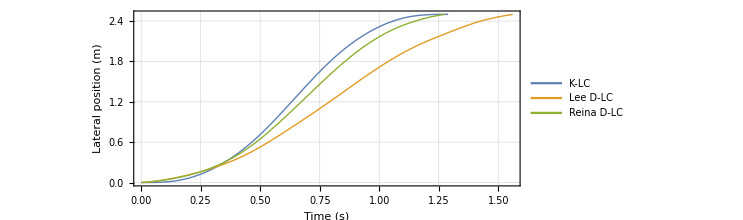

```mathematica
pNKD=ListLinePlot[{
Transpose@{Table[tt,{tt,0,tFKLC,tFKLC/(Length@nKLC-1)}], nKLC},
Transpose@{Table[tt,{tt,0,tF,tF/(Length@n-1)}], n},
Transpose@{Table[tt,{tt,0,tFReina,tFReina/(Length@n-1)}], nReina}
},
PlotLegends->Placed[LineLegend[{"K-LC","Lee D-LC","Reina D-LC"},LegendMarkerSize->10,LegendFunction->Frame,Background->White],{0.13,0.75}],
ImageSize->550,AspectRatio->0.4,
FrameLabel->{{Text[Style["Lateral position (m)",15,FontFamily->"Palatino",Black]],None}, {Text[Style["Time (s)",15,FontFamily->"Palatino",Black]],None}},PlotStyle->Thick, ImageSize->Large,Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
(*FrameTicks->{{{0,1.,2,2.5},None},{{0.5,1,1.5},None}},*)
ImagePadding->{{55,55},{45,3}},
FrameTicksStyle->{{14,Black},14}]
```

```mathematica
(*Export["/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/pNKD30.png", Rasterize[pNKD,"Image",RasterSize->3000]]*)
```

/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/pNKD30.png

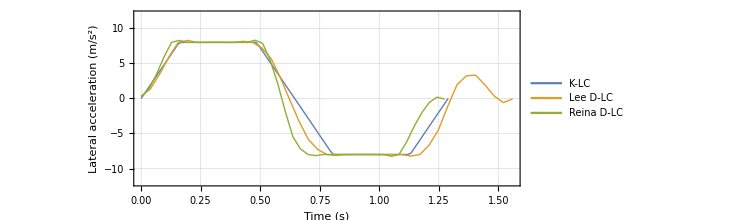

```mathematica
pAyKD=ListLinePlot[{
Transpose@{Table[tt,{tt,0,tFKLC,tFKLC/(Length@nKLC-1)}], ayKLC},
Transpose@{Table[tt,{tt,0,tF,tF/(Length@n-1)}], ay},
Transpose@{Table[tt,{tt,0,tFReina,tFReina/(Length@n-1)}], ayReina}
(*Transpose@{Table[tt,{tt,0,tFtmp,tFtmp/(Length@n-1)}], aytmp},*)
},
PlotLegends->Placed[LineLegend[{"K-LC","Lee D-LC","Reina D-LC"},LegendMarkerSize->10,LegendFunction->Frame,Background->White],{0.15,0.25}],
ImageSize->550,AspectRatio->0.4,PlotRange->{-12,12},
FrameLabel->{{Text[Style["Lateral acceleration (m/s^2)",15,FontFamily->"Palatino",Black]],None}, {Text[Style["Time (s)",15,FontFamily->"Palatino",Black]],None}},PlotStyle->Thick,Frame-> True,GridLines->Automatic,FrameStyle->Directive[Thickness[0.0025],Black],
(*FrameTicks->{{{-5,-2.5,0,2.5,5},None},{{0.5,1,1.5},None}},*)
ImagePadding->{{55,55},{45,5}},
FrameTicksStyle->{{14,Black},14}]
```

```mathematica
(*Export["/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/pAyKD30.png", Rasterize[pAyKD,"Image",RasterSize->3000]]*)
```

/Users/riccardodona/Documents/Work/JRC/activities/papers/preventable_lane_change/figures/pAyKD30.png